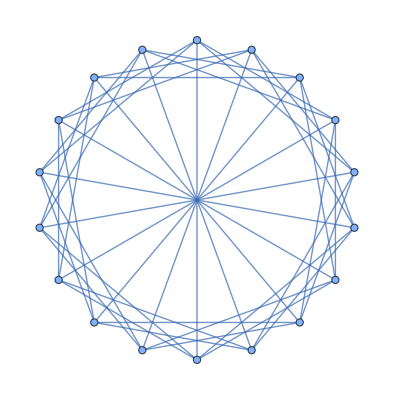

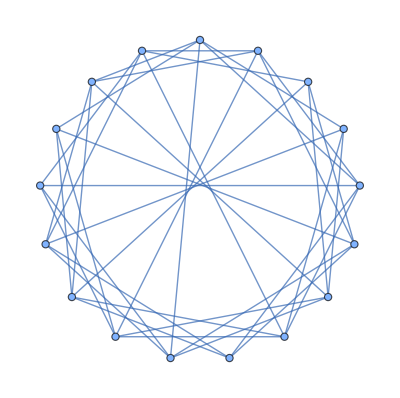

{{{1,4}},{{1,2,3,8,9,14}}}

```mathematica
s=17;k=2;v=5;
(*{2,3,9},{1,4,9}*)
cig=CirculantGraph[s+1,{3,4,9}]
g=VertexDelete[cig,s+1]
{FindClique[g],FindIndependentVertexSet[g]}
```

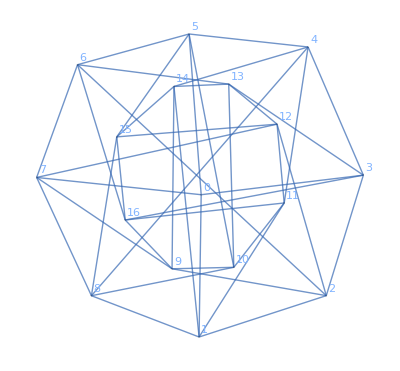

```mathematica
g=Import["E:\\cloud\\github\\a-boy\\playmath\\stage17-Ramsey-Numbers\\RamseyGraph17-R36--6-1.gv" ]
```

```mathematica
HamiltonianGraphQ[g]
VertexList@Graph[First@FindHamiltonianCycle[g]]
```

True

{5,0,1,11,10,9,16,6,13,3,2,12,7,8,15,14,4}

```mathematica
First@@%
```

5<->0

```mathematica
AcyclicGraphQ[g]
```

False

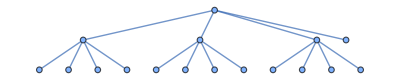

True

False

```mathematica
tree1=KaryTree[17,4]
IsomorphicSubgraphQ[KaryTree[17,3],g]
IsomorphicSubgraphQ[KaryTree[17,4],g]
```

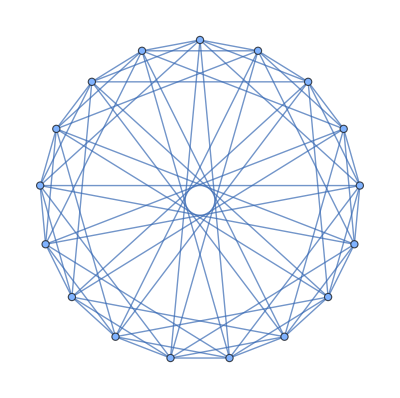

True

False

False

```mathematica
ci17=CirculantGraph[17,{1,2,4,8}]
IsomorphicSubgraphQ[KaryTree[17,5],ci17]
IsomorphicSubgraphQ[KaryTree[17,6],ci17]
```